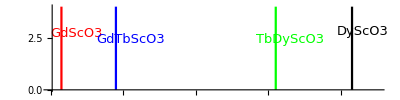

```mathematica
pl= ListLinePlot[{{{83,0},{83,6}},{{142,0},{142,6}},{{163,0},{163,6}},{{98,0},{98,6}}},PlotStyle->{Red,Green,Black,Blue},DataRange-> {75,200},  PlotRange-> {{80,170},{0,4}},AspectRatio->1/4, Axes-> {True, False}];
txtGd=Rotate[Text[Style["GdScO3", FontSize-> 13,FontColor->Red], {87,2.7}, {0,0}],Pi/2];
txtGdTb=Rotate[Text[Style["GdTbScO3",FontSize->13, FontColor-> Blue], {102,2.4}, {0,0}],Pi/2];
txtTbDy=Rotate[Text[Style["TbDyScO3",FontSize->13, FontColor->Green], {146,2.4}, {0,0}],π/2];
txtDy=Rotate[Text[Style["DyScO3",FontSize->13,FontColor->Black], {166,2.8}, {0,0}],π/2]; 
txt=Graphics[{txtGd, txtGdTb,txtTbDy,txtDy}];
Show[pl,txt]
```

```mathematica
.2
```